## Unit Square Graph paper

Fill in myMotief with your drawing.

This makes two images - one with graph paper, one without.
Save the non-graph paper version

Use “Save Selection As” under File to save your image.

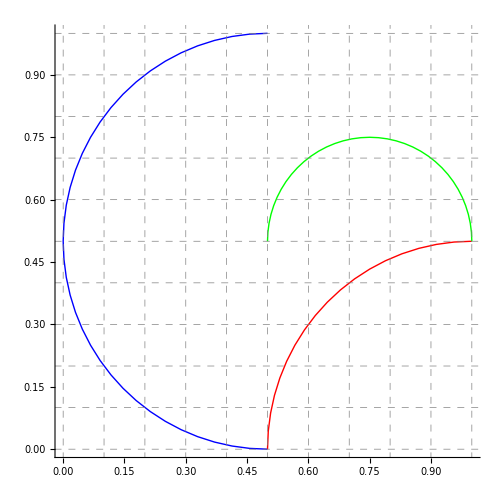

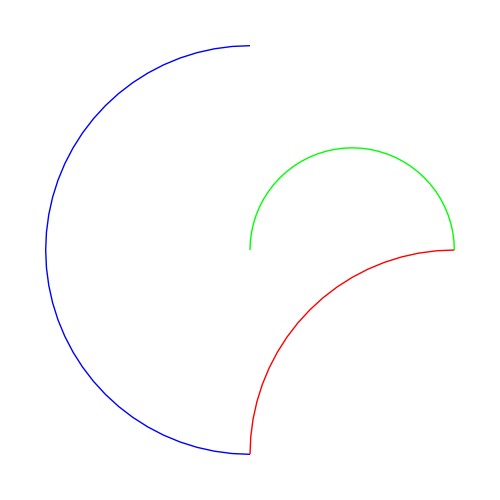

```mathematica
myMotief = {
			(*Circle[ {.3,.3}, .2],*)
			{Blue, Circle[{0.5, 0.5}, .5, {Pi/2, 3/2*Pi}]},
			{Red, Circle[{1, 0}, .5, {Pi/2, Pi}]},
			{Green, Circle[{0.75, 0.5}, .25, {0, Pi}]}
			(*Text[ "Fill in Your Own Design", {.5, 0.5} ]*)
		};

rotate90 = 
Graphics[
		{
			myMotief
	       },

		{
			PlotRange-> { {0,1}, {0,1} },
			AspectRatio -> 1,
			GridLines-> {  Range[0,1, .1], Range[0,1, 0.1] },
			GridLinesStyle -> Directive[ Gray, Dashed ],
			Axes-> True,
			ImageSize-> 500
	      }
		]



Graphics[
		{
			myMotief
	       },

		{
			PlotRange-> { {0,1}, {0,1} },
			AspectRatio -> 1,
			ImageSize-> 500
	      }
		]
```